```mathematica
f1 = E^(-(x-1)^2/ϵ)
```

ⅇ^(-(-1+x)^2/ϵ)

General::munfl: Exp[-999.918] is too small to represent as a normalized machine number; precision may be lost.

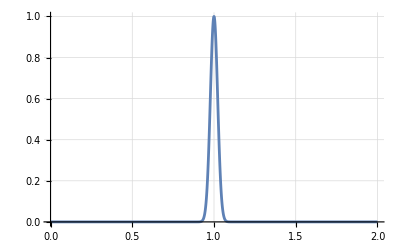

```mathematica
subst = ϵ->1*^-3;
Plot[f1/.subst, {x, 0, 2}, PlotRange->All, GridLines->Automatic]
```

```mathematica
intF1 = Integrate[f1/.subst, x]
intf1 = Integrate[f1/.subst, {x,0,2}]
%//N
```

1/20 √(π/10) Erf[10 √10 (-1+x)]

1/10 √(π/10) Erf[10 √10]

0.0560499

```mathematica
f2 = x Sin[1/x]
```

x Sin[1/x]

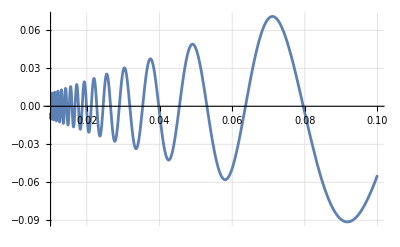

```mathematica
Plot[f2, {x, 1/100, 1/10}, GridLines->Automatic]
```

```mathematica
intF2 = Integrate[f2, x]
intf2 = Integrate[f2, {x, 1/100, 1/10}]
%//N
```

1/2 x Cos[1/x]+1/2 x^2 Sin[1/x]+1/2 SinIntegral[1/x]

Cos[10]/20-Cos[100]/200+Sin[10]/200-Sin[100]/20000+SinIntegral[10]/2-SinIntegral[100]/2

-0.000898894

```mathematica
f31 = 2x+5
f32 = (-5 π^2(x^2-2x-5)+10π x+2x)/(1+5 π^2)
f33 = 2Sin[2x] + (4 + 20 π^2+25 π^3)/(π + 5 π^3)-2Sin[4/π]
```

5+2 x

(2 x+10 π x-5 π^2 (-5-2 x+x^2))/(1+5 π^2)

(4+20 π^2+25 π^3)/(π+5 π^3)-2 Sin[4/π]+2 Sin[2 x]

Piecewise[{{5+2 x, 0≤x<1/π}, {(2 x+10 π x-5 π^2 (-5-2 x+x^2))/(1+5 π^2), 1/π≤x<2/π}, {(4+20 π^2+25 π^3)/(π+5 π^3)-2 Sin[4/π]+2 Sin[2 x], 2/π≤x≤8/π}, {0, True}}]

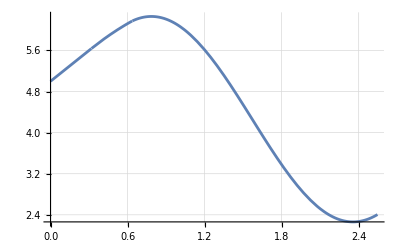

```mathematica
f3 = Piecewise[{{f31, 0<=x<1/π}, {f32, 1/π <=x<2/π}, {f33, 2/π<=x<=8/π}}]
Plot[f3, {x,0,8/π }, GridLines->Automatic]
```

```mathematica
intf31 = Integrate[f31, x]
intf32 = Integrate[f32, x]
intf33 = Integrate[f33, x]
```

5 x+x^2

(25 π^2 x+x^2+5 π x^2+5 π^2 x^2-(5 π^2 x^3)/3)/(1+5 π^2)

((4+20 π^2+25 π^3) x)/(π+5 π^3)-Cos[2 x]-2 x Sin[4/π]

```mathematica
intF3 = Integrate[f3, x]
intf3 = Integrate[f3, {x, 0, 8/π}];
%//N
```

Piecewise[{{0, x≤0}, {5 x+x^2, 0<x≤1/π}, {1/π^2+5/π-(5+1/π^2+10/(3 π)+25 π)/(1+5 π^2)+(25 π^2 x+x^2+5 π x^2+5 π^2 x^2-(5 π^2 x^3)/3)/(1+5 π^2), 1/π<x≤2/π}, {1/π^2+5/π-(5+1/π^2+10/(3 π)+25 π)/(1+5 π^2)+(20+4/π^2+20/(3 π)+50 π)/(1+5 π^2)-(8/π+40 π-(π+5 π^3) Cos[4/π]-4 Sin[4/π]-10 π^2 (-5+2 Sin[4/π]))/(π+5 π^3)+(4 x+20 π^2 x-(π+5 π^3) Cos[2 x]-2 π x Sin[4/π]-5 π^3 x (-5+2 Sin[4/π]))/(π+5 π^3), 2/π<x≤8/π}, {1/π^2+5/π-(5+1/π^2+10/(3 π)+25 π)/(1+5 π^2)+(20+4/π^2+20/(3 π)+50 π)/(1+5 π^2)+(32/π+160 π-(π+5 π^3) Cos[16/π]-16 Sin[4/π]-40 π^2 (-5+2 Sin[4/π]))/(π+5 π^3)-(8/π+40 π-(π+5 π^3) Cos[4/π]-4 Sin[4/π]-10 π^2 (-5+2 Sin[4/π]))/(π+5 π^3), True}}]

11.6391

```mathematica
intF3/.x->1/π//N
intF3/.x->2/π//N
intF3/.x->8/π//N
```

1.69287

3.57785

11.6391

```mathematica
intf32/.x->1/π
```

(5+1/π^2+10/(3 π)+25 π)/(1+5 π^2)

```mathematica
intf33/.x->2/π//Simplify//N
```

2.41997

```mathematica
(8/π+40 π-(π+5 π^3) Cos[4/π]-4 Sin[4/π]-10 π^2 (-5+2 Sin[4/π]))/(π+5 π^3)//N
```

2.41997

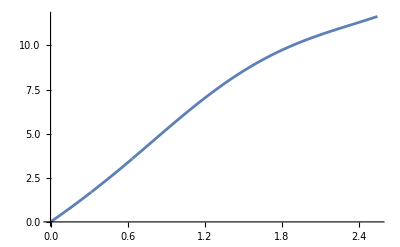

```mathematica
Plot[intF3, {x, 0, 8/π}]
```